## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/Mathematica_files/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)

(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="ert/mercury/figures/"; 
Get["utility modules.m",Path->dirPack];
stamp1;
```

CreateDirectory::filex: /Users/dantopa/Mathematica_files/io/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/mercury/ already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

maximum memory: 0.079869 GB

seed file: /Users/dantopa/Mathematica_files/nb/seed 19_12.nb

user: dantopa, CPU: Xiuhcoatl,  MM v. 12.0.0 for Mac OS X x86

date: Jan 26, 2020, time: 12:25:33

nb: /Users/dantopa/Mathematica_files/nb/ert/mercury/figures/seed 19_12.nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 0.079869 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

#### functions

#### substitutions

#### modules

## 1 waves

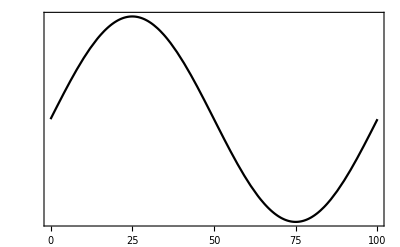

```mathematica
g001=Plot[Sin[π/50 x],{x,0,100},
Frame->True,
FrameTicks->{{ints,Automatic},{Automatic,Automatic}},
PlotStyle->Black,
Ticks->{Automatic,None}]
```

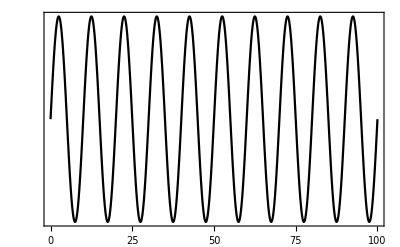

```mathematica
g002=Plot[Sin[π/5 x],{x,0,100},
Frame->True,
FrameTicks->{{ints,Automatic},{Automatic,Automatic}},
PlotStyle->Black,
Ticks->{Automatic,None}]
```

## 2

## 3

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```